```mathematica
PureIntegralsNEW=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis1-111.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
```

```mathematica
PureIntegralsNEW[[112;;]]//Length
ReduListT=PureIntegralsNEW[[112;;]]/.hxb[n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_]:>{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13};
Sectors=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
Sectors2=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) ;
RemainingSectors=SortBy[Tally[Sectors2],Last]
```

130

{{{0,0,1,1,0,0,1,1,0,0,0,0,0},1},{{0,0,1,1,0,1,0,1,0,0,0,0,0},1},{{0,0,1,1,0,1,1,1,0,0,0,0,0},1},{{0,1,0,1,0,0,1,1,0,0,0,0,0},1},{{0,1,0,1,0,1,1,1,0,0,0,0,0},1},{{0,1,0,1,1,1,0,1,0,0,0,0,0},1},{{0,1,0,1,1,1,1,1,1,0,0,0,0},1},{{0,1,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,0,1,0,0,1,1,0,0,0,0,0},1},{{1,0,0,1,0,1,1,1,0,0,0,0,0},1},{{1,0,0,1,1,1,0,1,0,0,0,0,0},1},{{1,0,1,1,0,0,1,1,1,0,0,0,0},1},{{1,0,1,1,0,1,0,1,1,0,0,0,0},1},{{1,0,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,1,0,1,1,0,0,0,0,0},1},{{1,0,1,1,1,1,0,1,0,0,0,0,0},1},{{1,0,1,1,1,1,1,1,0,0,0,0,0},1},{{1,1,0,1,1,1,1,1,0,0,0,0,0},1},{{1,1,1,1,1,1,1,1,1,0,0,0,0},1},{{0,0,1,1,0,0,1,1,1,0,0,0,0},2},{{0,0,1,1,0,1,0,1,1,0,0,0,0},2},{{0,0,1,1,0,1,1,1,1,0,0,0,0},2},{{0,1,0,1,0,0,1,1,1,0,0,0,0},2},{{0,1,0,1,0,1,0,1,0,0,0,0,0},2},{{0,1,0,1,0,1,0,1,1,0,0,0,0},2},{{0,1,0,1,0,1,1,1,1,0,0,0,0},2},{{0,1,0,1,1,0,1,1,0,0,0,0,0},2},{{0,1,0,1,1,0,1,1,1,0,0,0,0},2},{{0,1,0,1,1,1,0,1,1,0,0,0,0},2},{{0,1,0,1,1,1,1,1,0,0,0,0,0},2},{{0,1,1,1,0,0,1,1,0,0,0,0,0},2},{{0,1,1,1,0,0,1,1,1,0,0,0,0},2},{{0,1,1,1,0,1,0,1,0,0,0,0,0},2},{{0,1,1,1,0,1,0,1,1,0,0,0,0},2},{{0,1,1,1,0,1,1,1,0,0,0,0,0},2},{{1,0,0,1,0,1,0,1,0,0,0,0,0},2},{{1,0,0,1,1,0,1,1,0,0,0,0,0},2},{{1,0,0,1,1,1,1,1,0,0,0,0,0},2},{{1,1,0,1,0,0,1,1,0,0,0,0,0},2},{{1,1,0,1,0,1,0,1,0,0,0,0,0},2},{{1,1,0,1,0,1,1,1,0,0,0,0,0},2},{{1,1,0,1,1,0,1,1,0,0,0,0,0},2},{{1,1,0,1,1,1,0,1,0,0,0,0,0},2},{{1,1,1,1,0,1,1,1,1,0,0,0,0},3},{{1,1,1,1,1,0,1,1,1,0,0,0,0},3},{{1,1,1,1,1,1,0,1,0,0,0,0,0},3},{{1,1,1,1,1,1,0,1,1,0,0,0,0},3},{{1,1,1,1,1,1,1,1,0,0,0,0,0},3},{{1,1,1,1,0,0,1,1,1,0,0,0,0},4},{{1,1,1,1,0,1,0,1,1,0,0,0,0},4},{{1,1,1,1,1,0,1,1,0,0,0,0,0},4},{{1,1,1,1,0,0,1,1,0,0,0,0,0},5},{{1,0,1,1,0,0,1,1,0,0,0,0,0},6},{{1,0,1,1,0,1,0,1,0,0,0,0,0},6},{{1,0,1,1,0,1,1,1,0,0,0,0,0},6},{{1,1,1,1,0,1,0,1,0,0,0,0,0},6},{{1,1,1,1,0,1,1,1,0,0,0,0,0},7}}

```mathematica
Position[Sectors2/.{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_}:>hxb[n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13],RemainingSectors[[9,1]]/.List->hxb]+111
```

{{155}}

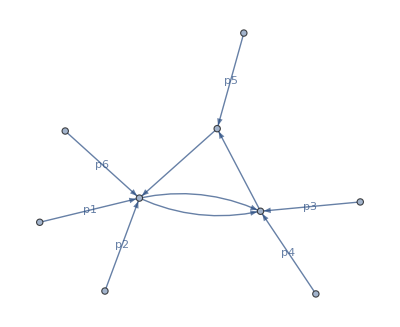
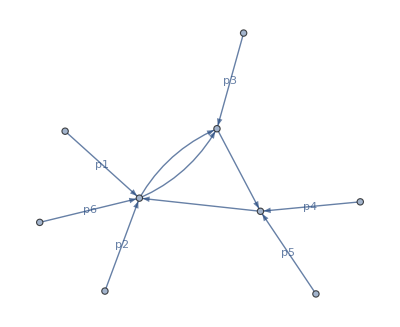
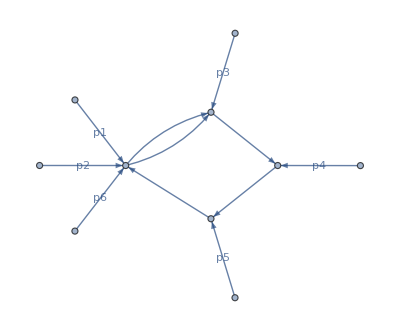
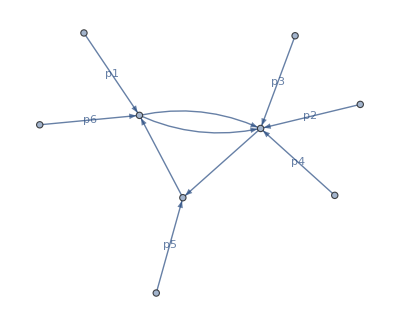
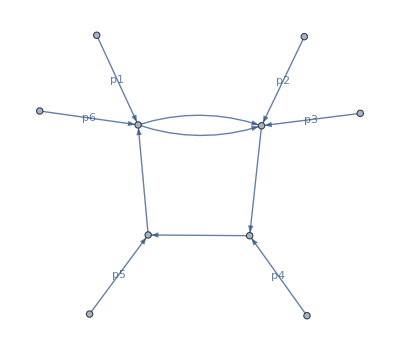
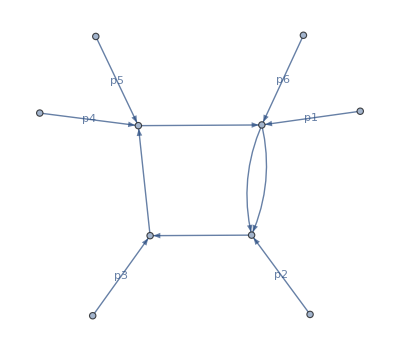
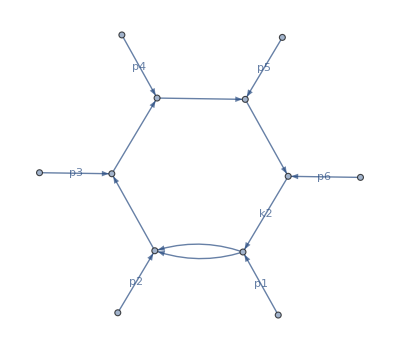
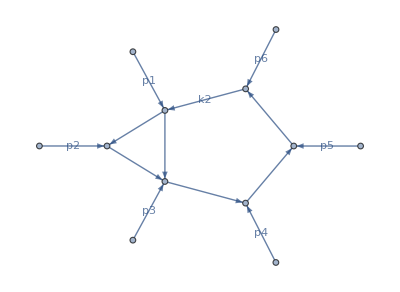
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

{{132}}

hxb[0,1,0,1,0,0,1,1,0,0,0,0,0]

```mathematica
PlotDiagrams=Table[plotDiagram[RemainingSectors[[i,1]]],{i,1,Length[RemainingSectors]}];
Grid[ArrayReshape[PlotDiagrams,{17,3}]]
```